# Midterm

León Ocaña^1, Yordan Solórzano^2, Luis Macas^1, Juan Diego Vizcaino^1

^1Group #2, School of Physical Science and Nanotechnology, Yachay Tech University, Urcuqui - Ecuador

```mathematica
wrkdir=
"/Users/luismacas/wrk/Final/input";
SetDirectory[wrkdir];
```

### Analysis of ENCUT

```mathematica
datair = Import["ecut.dat"]//Map[#/{1,2}&,#]&
```

{{200,-8.92251},{250,-9.1958},{300,-9.16174},{350,-9.10964},{400,-9.09656},{450,-9.09329},{500,-9.09121},{550,-9.09212},{600,-9.09382},{650,-9.09563},{700,-9.09637},{750,-9.09768},{800,-9.09862},{850,-9.09921},{900,-9.09932}}

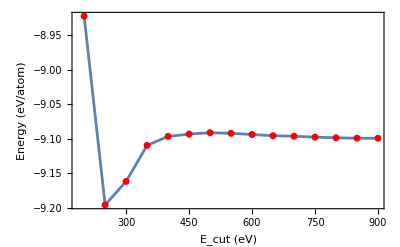

```mathematica
ListPlot[datair,
Frame->True,
FrameLabel->{"E_cut (eV)","Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->400,
Epilog->{Red,AbsolutePointSize[5],Point[datair]}
]
```

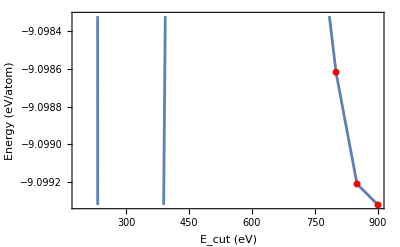

```mathematica
ListPlot[datair,
Frame->True,
FrameLabel->{"E_cut (eV)","Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Joined->True,
PlotRange->{-9.09932082,-9.09932082+10^-3},
InterpolationOrder->1,
ImageSize->400,
Epilog->{Red,AbsolutePointSize[5],Point[datair]}
]
```

{{800.0823801781748, -9.09861921897612}} point is inside of the 1 meV/atom window. Ecut is 800eV.
We chose the 1meV/atom criteria to ensure the external influence of magnetic properties of material is neglected

### Analysis of k - points

```mathematica
datakp = Import["kps.dat"]//Map[#/{1,2}&,#]&
```

{{3,-8.80668},{4,-9.03185},{5,-9.08148},{6,-9.09395},{7,-9.09729},{8,-9.09826},{9,-9.09853},{10,-9.09862},{11,-9.09865},{12,-9.09867}}

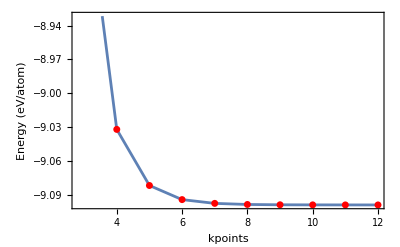

```mathematica
ListPlot[datakp,
Frame->True,
FrameLabel->{"kpoints","Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Joined->True,
InterpolationOrder->1,
ImageSize->400,
Epilog->{Red,AbsolutePointSize[5],Point[datakp]}
]
```

Analising the convergency of k - points

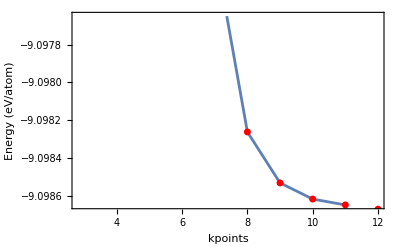

```mathematica
ListPlot[datakp,
Frame->True,
FrameLabel->{"kpoints","Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Joined->True,
PlotRange->{-9.098648655,-9.098648655+10^-3},
InterpolationOrder->1,
ImageSize->400,
Epilog->{Red,AbsolutePointSize[5],Point[datakp]}
]
```

The convergency is for 8 k-points

For the k points grid we will use 8x8x8 to converge the energy to <1meV/atom

We know that for any crystal shape, the volume can be computed like:

```mathematica
Range[val-3,val+5,0.5]/.val->14.0//Map[(#//ToString)<>" "&,#]&//StringJoin
```

11. 11.5 12. 12.5 13. 13.5 14. 14.5 15. 15.5 16. 16.5 17. 17.5 18. 18.5 19.

```mathematica
cell= Import["cell.dat"][[All,{1,2}]]
```

{{8.4,-16.5001},{8.9,-17.1168},{9.4,-17.5631},{9.9,-17.8689},{10.4,-18.0639},{10.9,-18.1686},{11.4,-18.2004},{11.9,-18.1721},{12.4,-18.0957},{12.9,-17.9803},{13.4,-17.8334},{13.9,-17.6596},{14.4,-17.4662}}

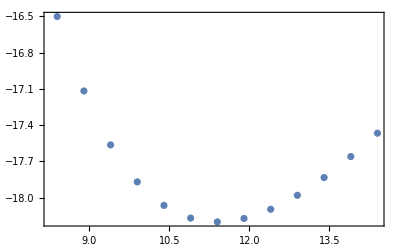

```mathematica
cell//ListPlot[#,Frame->True]&
```

```mathematica
eos=e0+(9 v0 B0)/16(((v0/v)^(2/3)-1)^3 B0'+((v0/v)^(2/3)-1)^2(6-4((v0/v)^(2/3))));
```

Fitting of the equation of the state

```mathematica
NonlinearModelFit[cell,eos,{e0,v0,B0,B0'},v]
```

NonlinearModelFit::nrlnum: The function value {-42.7063+84.9419 ⅈ,-42.6733+80.6957 ⅈ,-42.678+76.9001 ⅈ,-42.7192+73.4858 ⅈ,-42.7885+70.3971 ⅈ,-«18»+«1»,-42.9952+65.0235 ⅈ,-43.1254+62.6705 ⅈ,-43.2687+60.5037 ⅈ,-43.4224+58.5016 ⅈ,«3»} is not a list of real numbers with dimensions {13} at {e0,v0,B0,B0'} = {-5.35544,-2.77806,-2.26337,18.1934}.

FittedModel[-5.35544+3.53687 ((6-7.90475 (-1/v)^(2/3)) (-1+1.97619 «1»)^2+18.1934 (-1+«1»)^3)]

```mathematica
eos//PowerExpand//ExpandAll//Collect[#,v]&
```

e0+(27 B0 v0)/8-9/16 B0 v0 B0'+(-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B0')/v^(2/3)+(63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B0')/v^(4/3)+(-(9 B0 v0^3)/4+9/16 B0 v0^3 B0')/v^2

```mathematica
model=k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
```

```mathematica
parameters=Table[k[i],{i,4}]
```

{k[1],k[2],k[3],k[4]}

```mathematica
nlm=NonlinearModelFit[cell,model,parameters,v]
```

FittedModel[21.5688-679.42/v^2+1288.57/v^(4/3)-429.35/v^(2/3)]

```mathematica
nlm[v]
```

21.5688-679.42/v^2+1288.57/v^(4/3)-429.35/v^(2/3)

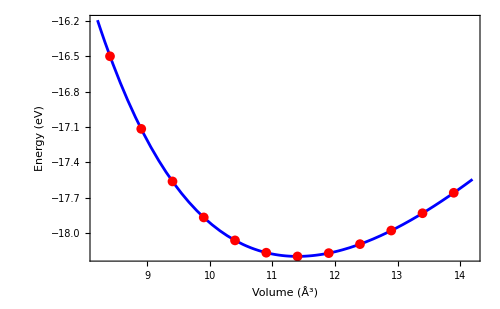

```mathematica
Plot[nlm[v],{v,(cell[[All,1]]//Min)-0.2,(cell[[All,1]]//Max)-0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)","Energy (eV)"},
PlotStyle->{AbsoluteThickness[2],Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cell]}
]
```

```mathematica
nlm["RSquared"]
```

1.

```mathematica
opVol=FindMinimum[nlm[v],
{v,11.41}]
```

{-18.1997,{v→11.3996}}

```mathematica
{-18.199729299951727,{v->11.3996}}
```

{-18.1997,{v→11.3996}}

Bulk modulus

```mathematica
B0=v D[nlm[v],{v,2}]/.opVol[[2]]//UnitConvert[
Quantity[#,("Electronvolts")/("Angstroms")^3],
"GigaPascals"]&(*Converting to GigaPascals as the original units are eV/Å^3*)
```

431.513 GPa

```mathematica
B0=v D[nlm[v],{v,2}]/.opVol[[2]];
B0'=-v/B0 D[v D[nlm[v],{v,2}],v]/.opVol[[2]](*Bulk Modulus pressure derivative*)
```

3.69726

Other way to get the mechanical properties of a crystal from the EOS.

```mathematica
nlm["BestFitParameters"]
```

{k[1]→21.5688,k[2]→-429.35,k[3]→1288.57,k[4]→-679.42}

```mathematica
Clear[B0]
```

```mathematica
sol=Solve[{e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlm["BestFitParameters"],{e0,B0,v0,B'}]
```

{{e0→205.133,B0→-988.245,v0→0.907367,B'→5.63607},{e0→-18.1997,B0→2.69329,v0→11.3996,B'→3.69726}}

```mathematica
Solve[v0==a0^3/4,a0]/.sol
```

{{{a0→-0.768395+1.3309 ⅈ},{a0→1.53679},{a0→-0.768395-1.3309 ⅈ}},{{a0→-1.78629+3.09395 ⅈ},{a0→3.57259},{a0→-1.78629-3.09395 ⅈ}}}

```mathematica
B0comp=UnitConvert[
Quantity[2.693292035553483,("Electronvolts")/("Angstroms")^3],
"GigaPascals"]
```

431.513 GPa

### The density of states (DOS) and partial density of states (PDOS)

```mathematica
input=Import["DOSCAR","Table"];
```

```mathematica
dos=input[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input[[6,4]]
```

9.70573

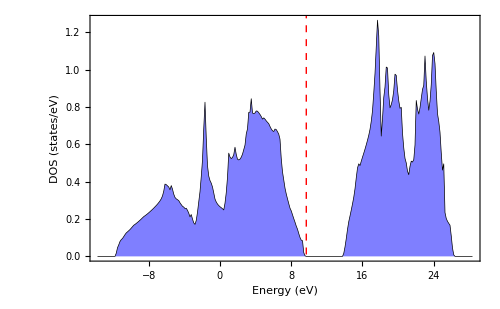

```mathematica
ListPlot[dos,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
GridLines->{{ef},None},
GridLinesStyle->
Directive[Red,Dashed,
AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500]
```

Now we are going to analyze the PDOS, we have to consider this:

energy s p_y p_z p_x

```mathematica
dos1=input[[7+300+2;;7+300+2+300]];
dos2=input[[7+300+2+300+2;;7+300+2+300+2+300]];
```

```mathematica
dosall=(dos1+dos2)//Map[#/{2,1,1,1,1,1,1,1,1,1}&,#]&;
```

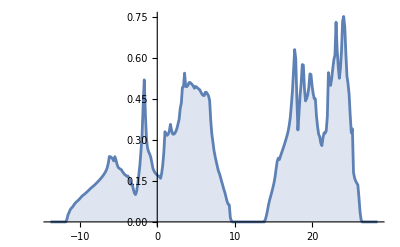

```mathematica
f[total]=Map[{#[[1]],Plus@@(#[[2;;10]])}&,
#]&;
f[s]=Map[{#[[1]],#[[2]]}&,#]&;
f[p]=Map[{#[[1]],Plus@@(#[[3;;5]])}&,#]&;
dosall//f[total]//
ListPlot[#,Joined->True,Filling->Axis]&
```

The s-states will be

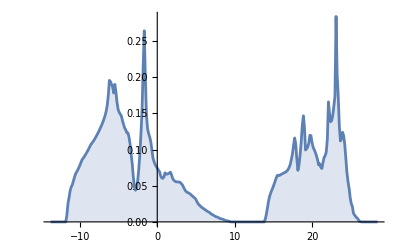

```mathematica
dosall//f[s]//
ListPlot[#,Joined->True,Filling->Axis]&
```

For p-states

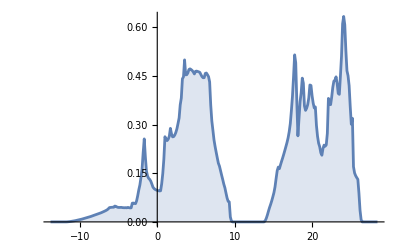

```mathematica
dosall//f[p]//
ListPlot[#,Joined->True,Filling->Axis]&
```

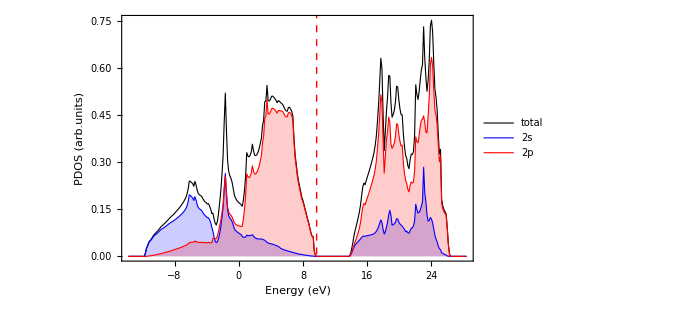

```mathematica
{dosall//f[total],dosall//f[s],dosall//f[p]}//ListPlot[#,
Joined->True,
GridLines->{{ef},None},
Filling->{2->Axis,3->Axis, 4->Axis},
Frame->True,
FrameLabel->{"Energy (eV)","PDOS (arb.units)"},
PlotRange->All,
PlotLegends->Placed[{"total","2s","2p"},{Scaled[{0,0.75}],{0,0.5}}],
ImageSize->500,
Axes->None,
GridLinesStyle->
Directive[Red, Dashed,
AbsoluteThickness[1.0]],
PlotStyle->
{{AbsoluteThickness[0.8],Black}, 
{AbsoluteThickness[0.8],Blue},
{AbsoluteThickness[0.8],Red}, 
{AbsoluteThickness[0.8],Green}},
BaseStyle->{FontFamily->"Helvetica", 
FontSize->18}
]&
```

Is the system metal, semiconductor or insulator?

The system is an insulator due to there is a bandgap

### The band structure of Ir using PROCAR_OPT file

```mathematica
(*define the Fermi elevel take from previous calculations*)
ef =input[[6,4]]
```

9.70573

```mathematica
ef=input[[6,4]];
```

```mathematica
Run["grep k-point PROCAR_OPT > kpt"];
Run["sed 's/-/ -/g' kpt > kpt2"];
Run["sed 's/k -point/k-point/g' kpt2 > kpts"];
Run["rm kpt kpt2"];
Run["grep band PROCAR_OPT > bandData"];
Run["grep \"# of bands\" PROCAR_OPT | tail -1 > numbands"];
```

```mathematica
(*This gets number of kp and bands*)
bandsinfo=Import["numbands","Table"][[1]];
{Nkpt,Nbands}=bandsinfo//{#[[4]],#[[8]]}&
```

{140,8}

```mathematica
(*This gets the high symmetry points and divisions*)
path=Import["KPOINTS-bs","Table"];
div=path[[2,1]];
```

```mathematica
(*This defines the high symmetry points labels and the length*)
hsympts=(If[(path[[5]]//Length)==4,path[[5;;-1]]//Flatten//Partition[#,4]&//#[[All,4]]&, path[[5;;-1]]//Flatten//Partition[#,5]&//#[[All,5]]&]//Drop[#,{3,Length[#],2}]&)/."GAMMA"->"Γ"
NumGridL=(hsympts//Length)-2;
```

{L,Γ,X,K,Γ}

```mathematica
(*This defines the band energies shifted to Ef*)
bands=Import["bandData","Table"][[2;;-1]][[All,5]]-ef//Partition[#,Nbands]&;
bandener=bands//Drop[#,{div,Nkpt-div,div}]&;
```

```mathematica
(*This defines k-point coordinates*)
kp=Import["kpts","Table"][[2;;-1]][[All,{4,5,6}]];
kpt=kp//Drop[#,{div,Nkpt-div,div}]&;
```

```mathematica
(*This liniarizes k-point coordinates in 1D*)
kpt2=Join[{0},Table[Norm[kpt[[i+1]]-kpt[[i]]],{i,(kpt//Length)-1}]]//Accumulate;
```

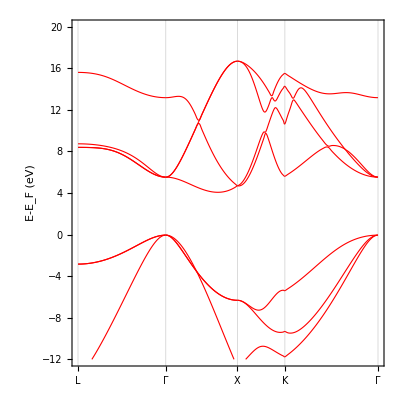

```mathematica
(*This creates the bands in kpt2 domain*)
bands2={kpt2,bandener}//Transpose;
Do[bd[i]=bands2//Map[{#[[1]],#[[2,i]]}&,#]&,{i,Nbands}];

(*please provide the bands you want to plot*)
ListPlot[Table[bd[i],{i,1,8(*Nbands*)}],
Frame->True,
FrameLabel->{"","E-E_F (eV)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->14},
Joined->True,
InterpolationOrder->2,
AspectRatio->1,
AxesStyle->Directive[Black,Dashed, AbsoluteThickness[0.7]],
FrameTicks->{{Automatic,None},{{kpt2[[Join[Table[i div-(i-1),{i,0,NumGridL}],{-1}]]],hsympts}//Transpose,None}},
GridLines->{kpt2[[Join[Table[i div-(i-1),{i,0,NumGridL}],{-1}]]],None},
PlotStyle->Directive[Red,AbsoluteThickness[0.8]],
PlotRange->{{0,kpt2[[-1]]},{-12,20}}]
```

## Diamond Surface

```mathematica
bulk=Import["POSCAR-bulk","Table"];
```

```mathematica
lattbulk=bulk[[2,1]]bulk[[3;;5]]
```

{{2.5262,0.,0.},{1.2631,2.18776,0.},{1.2631,0.729252,2.06264}}

```mathematica
{a,b,c}=lattbulk;
Δk=Table[0.07-0.005i,{i,0,10}];
```

```mathematica
Δk//Map[{#,Round[((b×c)/((a×b).c)//Norm)/#],
Round[((c×a)/((a×b).c)//Norm)/#],
Round[((a×b)/((a×b).c)//Norm)/#]}&,#]&//TableForm
```

0.07 | 7 | 7 | 7
0.065 | 7 | 7 | 7
0.06 | 8 | 8 | 8
0.055 | 9 | 9 | 9
0.05 | 10 | 10 | 10
0.045 | 11 | 11 | 11
0.04 | 12 | 12 | 12
0.035 | 14 | 14 | 14
0.03 | 16 | 16 | 16
0.025 | 19 | 19 | 19
0.02 | 24 | 24 | 24

```mathematica
po1x2=Import["POSCAR-1x2l5v10-init.POSCAR","Table"];
```

```mathematica
lattpo1x2=po1x2[[2,1]]po1x2[[3;;5]]
```

{{2.5262,0.,0.},{0.,5.0524,0.},{0.,0.,14.5726}}

```mathematica
{a,b,c}=lattpo1x2;
Δk=Table[0.07-0.005i,{i,0,10}];
```

```mathematica
Δk//Map[{#,Round[((b×c)/((a×b).c)//Norm)/#],
Round[((c×a)/((a×b).c)//Norm)/#],
Round[((a×b)/((a×b).c)//Norm)/#]}&,#]&//TableForm
```

0.07 | 6 | 3 | 1
0.065 | 6 | 3 | 1
0.06 | 7 | 3 | 1
0.055 | 7 | 4 | 1
0.05 | 8 | 4 | 1
0.045 | 9 | 4 | 2
0.04 | 10 | 5 | 2
0.035 | 11 | 6 | 2
0.03 | 13 | 7 | 2
0.025 | 16 | 8 | 3
0.02 | 20 | 10 | 3

### Change of the energy per atom VS vacuum size

```mathematica
vac=Import["vacuum.dat"]//Map[#/{1,5}&,#]&
```

{{5.,-7.72463},{6.,-7.72198},{7.,-7.72123},{8.,-7.72109},{9.,-7.72106},{10.,-7.72114},{11.,-7.72092},{12.,-7.72099},{13.,-7.72105},{14.,-7.72104},{15.,-7.72105}}

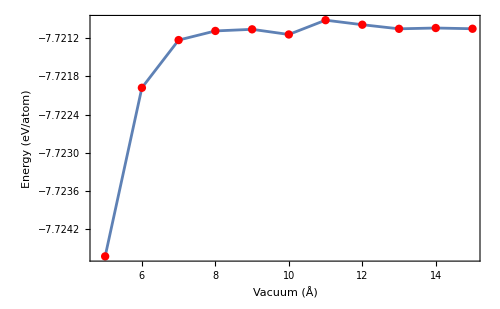

```mathematica
vac//ListPlot[#,
Frame->True,
FrameLabel->{"Vacuum (Å)","Energy (eV/atom)"},
Axes->False,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
Joined->True,
ImageSize->500,
PlotRange->All,
Epilog->{Red,AbsolutePointSize[6],
Point[#]}
]&
```

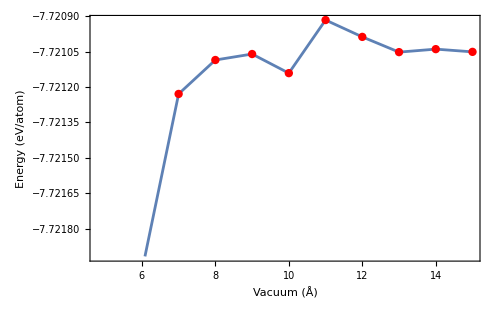

```mathematica
vac//ListPlot[#,
Frame->True,
FrameLabel->{"Vacuum (Å)","Energy (eV/atom)"},
Axes->False,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
Joined->True,
ImageSize->500,
PlotRange->{-7.720917062173259,-7.720917062173259-10^-3},
PlotRange->All,
Epilog->{Red,AbsolutePointSize[6],
Point[#]}
]&
```

### Surface energies

```mathematica
surfen=Import["surfaces.dat"][[All,{1,2}]];
surfen//TableForm
```

1x1l5v10 | -47.4014
1x2l5v10 | -97.71
1x2l5v10b | -97.7098

To compute the surface energy, we use:

```mathematica
A1x1=2.526199^2;
A1x2= 2.52619 5.052399;
A1x2b=2.52619 5.052399;
```

```mathematica
e[C]=-18.20036/2;
e[h]=-3.3858;
```

```mathematica
area={A1x1,A1x2,A1x2b};
```

```mathematica
nc={5,10,10};
nh={2,4,4};
```

```mathematica
results=Table[{surfen[[i,1]],area[[i]]//NumberForm[#,{4,2}]&,10^3 1/(2 area[[i]])(surfen[[i,2]]-nc[[i]]e[C]-nh[[i]]e[h])//NumberForm[#,{4,2}]&},{i,3}]
```

{{1x1l5v10,6.38,381.60},{1x2l5v10,12.76,267.80},{1x2l5v10b,12.76,267.80}}

```mathematica
Join[{{"Slab","A (Å^2)","E_sf(meV/Å^2)"}},
results]//TableForm
```

Slab | A (Å^2) | E_sf(meV/Å^2)
1x1l5v10 | 6.38 | 381.60
1x2l5v10 | 12.76 | 267.80
1x2l5v10b | 12.76 | 267.80

### DOS of C(100) surfaces

```mathematica
input1x1=Import["DOSCAR-1x1l5v10.st","Table"];
```

```mathematica
dos1x1=input1x1[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input1x1[[6,4]]
```

0.0675728

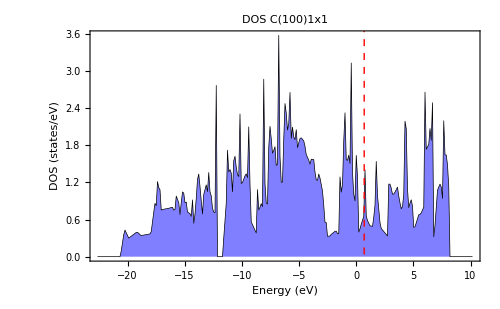

```mathematica
ListPlot[dos1x1,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
GridLines->{{ef},None},
GridLinesStyle->
Directive[Red,Dashed,
AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotLabel->"DOS C(100)1x1",
PlotRange->All]
```

```mathematica
input1x2=Import["DOSCAR-1x2l5v10.st","Table"];
```

```mathematica
dos1x2=input1x2[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input1x2[[6,4]]
```

0.723263

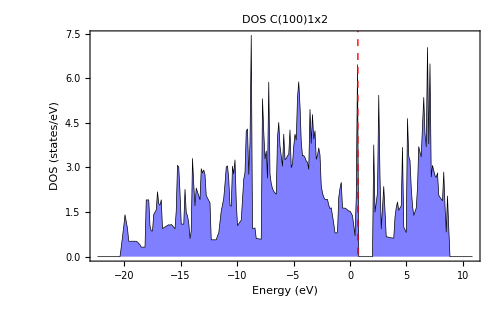

```mathematica
ListPlot[dos1x2,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
GridLines->{{ef},None},
GridLinesStyle->
Directive[Red,Dashed,
AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotLabel->"DOS C(100)1x2",
PlotRange->All]
```

```mathematica
input1x2b=Import["DOSCAR-1x2l5v10b.st","Table"];
```

```mathematica
dos1x2b=input1x2b[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input1x2b[[6,4]]
```

0.70069

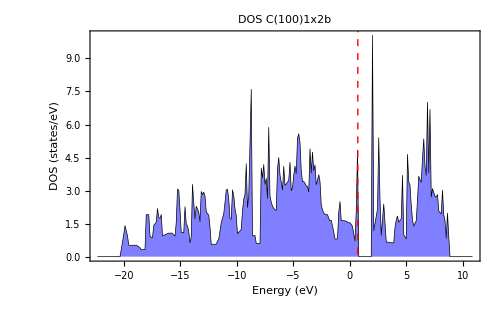

```mathematica
ListPlot[dos1x2b,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
GridLines->{{ef},None},
GridLinesStyle->
Directive[Red,Dashed,
AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotLabel->"DOS C(100)1x2b",
PlotRange->All]
```

## Generation of STM Images for C(100) - 1x2 (-2)

```mathematica
wrkdir=
"/Users/luismacas/wrk/Final/input";
SetDirectory[wrkdir];
```

```mathematica
in=Import["PARCHG-1x2l5v10b-2.vasp","Table"];
```

```mathematica
numat=Plus@@in[[7]]
```

14

```mathematica
thelattice=in[[3;;5]]
```

{{2.5262,0.,0.},{0.,5.0524,0.},{0.,0.,14.5726}}

```mathematica
in[[7+numat+3]]
```

{36,72,216}

```mathematica
stm=(in[[7+numat+4;;-1]]//Flatten);
```

```mathematica
stm//Dimensions
```

{559872}

```mathematica
stm[[1]]
```

0.2755

```mathematica
stm[[-1]]
```

0.27266

```mathematica
divX=in[[7+numat+3,1]]
```

36

```mathematica
divY=in[[7+numat+3,2]]
```

72

```mathematica
zrange=in[[5,{2,3}]]
```

{0.,14.5726}

```mathematica
transformDATA=
(
#
//Partition[#,divX]&
//Partition[#,divY]&
//Map[Append[#,First[#]]&,
#,{2}]&
//Map[Append[#,First[#]]&,#]&
//Transpose[#,{3,2,1}]&
)&;
```

```mathematica
stm1=stm//transformDATA;
```

```mathematica
stm1[[1,1]][[1]]
```

0.2755

```mathematica
stm1//Dimensions
```

{37,73,216}

### Here the interpolation for stm1

```mathematica
theInterpolation=ListInterpolation[#,{{0,in[[3,1]]},{0,in[[4,2]]},{0,in[[5,3]]}},PeriodicInterpolation->{True,True,False}]&;
```

```mathematica
stminterpolation=stm1//theInterpolation;
```

```mathematica
stminterpolation[0,0,3]
```

11.2117

```mathematica
nx=4;
ny=3;
ContourPlot3D[stminterpolation[x,y,z]==0.02,
{x,0,nx thelattice[[1,1]]},
{y,0,ny thelattice[[2,2]]},
{z,7,10},
ColorFunction->Function[{x,y,z,f},
ColorData["SunsetColors"][z]],
PlotPoints->30,
MaxRecursion->0,
BoxRatios->{1, (ny thelattice[[2,2]])/(nx thelattice[[1,1]]),(10-7)/(nx thelattice[[1,1]])},
AxesLabel->{"x(Å)","y(Å)",None},
ViewPoint->{0,0,∞},
BaseStyle->{FontFamily->"Helvetica",FontSize->13},
ContourStyle->Directive[Opacity[1.]],
Lighting->AmbientLight[GrayLevel[1.]],
Mesh->None]
```

-Graphics3D-

## Generation of STM Images for C(100) - 1×2

```mathematica
wrkdir=
"/Users/luismacas/wrk/Final/input";
SetDirectory[wrkdir];
```

```mathematica
in=Import["PARCHG-1x2l5v10b.vasp","Table"];
```

```mathematica
numat=Plus@@in[[7]]
```

14

```mathematica
thelattice=in[[3;;5]]
```

{{2.5262,0.,0.},{0.,5.0524,0.},{0.,0.,14.5726}}

```mathematica
in[[7+numat+3]]
```

{36,72,216}

```mathematica
stm=(in[[7+numat+4;;-1]]//Flatten);
```

```mathematica
stm//Dimensions
```

{559872}

```mathematica
stm[[1]]
```

0.89129

```mathematica
stm[[-1]]
```

1.0556

```mathematica
divX=in[[7+numat+3,1]]
```

36

```mathematica
divY=in[[7+numat+3,2]]
```

72

```mathematica
zrange=in[[5,{2,3}]]
```

{0.,14.5726}

```mathematica
transformDATA=
(
#
//Partition[#,divX]&
//Partition[#,divY]&
//Map[Append[#,First[#]]&,
#,{2}]&
//Map[Append[#,First[#]]&,#]&
//Transpose[#,{3,2,1}]&
)&;
```

```mathematica
stm1=stm//transformDATA;
```

```mathematica
stm1[[1,1]][[1]]
```

0.89129

```mathematica
stm1//Dimensions
```

{37,73,216}

### Here the interpolation for stm1

```mathematica
theInterpolation=ListInterpolation[#,{{0,in[[3,1]]},{0,in[[4,2]]},{0,in[[5,3]]}},PeriodicInterpolation->{True,True,False}]&;
```

```mathematica
stminterpolation=stm1//theInterpolation;
```

```mathematica
stminterpolation[0,0,3]
```

0.464574

```mathematica
nx=3;
ny=2;
ContourPlot3D[stminterpolation[x,y,z]==0.023,
{x,0,nx thelattice[[1,1]]},
{y,0,ny thelattice[[2,2]]},
{z,6,8.5},
ColorFunction->Function[{x,y,z,f},
ColorData["SunsetColors"][z]],
PlotPoints->30,
MaxRecursion->0,
BoxRatios->{1, (ny thelattice[[2,2]])/(nx thelattice[[1,1]]),(8.5-6)/(nx thelattice[[1,1]])},
AxesLabel->{"x(Å)","y(Å)",None},
ViewPoint->{0,0,∞},
BaseStyle->{FontFamily->"Helvetica",FontSize->13},
ContourStyle->Directive[Opacity[1.]],
Lighting->AmbientLight[GrayLevel[1.]],
Mesh->None]
```

-Graphics3D-